```mathematica
List[a,b,c,d]
```

{a,b,c,d}

```mathematica
{a,b,c,d}
```

{a,b,c,d}

```mathematica
FullForm[{a,b,c,d}]
```

List[a,b,c,d]

```mathematica
v = {1,2.3,x+4}
```

{1,2.3,4+x}

```mathematica
VectorQ[v]
```

True

```mathematica
v.v
```

6.29+(4+x)^2

```mathematica
m={{1,2,3},{1,4,9}}
```

{{1,2,3},{1,4,9}}

```mathematica
MatrixQ[m]
```

True

```mathematica
m.Transpose[m]
```

{{14,36},{36,98}}

```mathematica
Det[Transpose[m].m]
```

0

```mathematica
Transpose[m].m
```

{{2,6,12},{6,20,42},{12,42,90}}

```mathematica
ra = {{{1,2,3},{4,5,6}},{{7,8,9},{10,11,12}},{{13,14,15},{16,17,18}},{{19,20,21},{22,23,24}}}
```

{{{1,2,3},{4,5,6}},{{7,8,9},{10,11,12}},{{13,14,15},{16,17,18}},{{19,20,21},{22,23,24}}}

```mathematica
MatrixQ[ra]
```

False

```mathematica
ArrayQ[ra]
```

True

```mathematica
ra.{1,2,3}
```

{{14,32},{50,68},{86,104},{122,140}}

```mathematica
Fourier[ra]
```

{{{61.2372+0. ⅈ,-2.44949-1.41421 ⅈ,-2.44949+1.41421 ⅈ},{-7.34847+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}},{{-14.6969-14.6969 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}},{{-14.6969+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}},{{-14.6969+14.6969 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}}

```mathematica
ragged = {{1,2,3},{4,5},{6}}
```

```mathematica
{{1,2,3},{4,5},{6}}
```

{{1,2,3},{4,5},{6}}

```mathematica
ragged[[All,1]]
```

{1,4,6}

```mathematica
Map[Total,ragged]
```

{6,9,6}

```mathematica
PadRight[ragged]
```

{{1,2,3},{4,5,0},{6,0,0}}

```mathematica
PadLeft[ragged]
```

{{1,2,3},{0,4,5},{0,0,6}}

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Range[4,-4,-2]
```

{4,2,0,-2,-4}

```mathematica
Range[0.,1.,.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Array[f,4]
```

{f[1],f[2],f[3],f[4]}

```mathematica
Array[2^#&,4]
```

{2,4,8,16}

```mathematica
h[i_,j_]:=1/(i+j-1)
```

```mathematica
Array[h,{4,3}]
```

{{1,1/2,1/3},{1/2,1/3,1/4},{1/3,1/4,1/5},{1/4,1/5,1/6}}

```mathematica
Table[f[i],{i,4}]
```

{f[1],f[2],f[3],f[4]}

```mathematica
Table[2^i,{i,-4,4}]
```

{1/16,1/8,1/4,1/2,1,2,4,8,16}

```mathematica
Table[h[i,j],{i,4},{j,3}]
```

{{1,1/2,1/3},{1/2,1/3,1/4},{1/3,1/4,1/5},{1/4,1/5,1/6}}

```mathematica
Table[h[i,j],{i,4},{j,i}]
```

{{1},{1/2,1/3},{1/3,1/4,1/5},{1/4,1/5,1/6,1/7}}

```mathematica
NestList[3#(1-#)&,.1,20]
```

{0.1,0.27,0.5913,0.724993,0.598135,0.721109,0.603333,0.717967,0.607471,0.71535,0.610873,0.713121,0.613738,0.711191,0.616195,0.709496,0.618334,0.707991,0.620219,0.706642,0.621897}

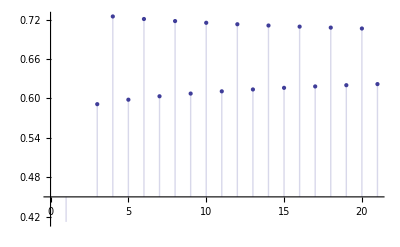

```mathematica
ListPlot[%,Filling->Axis]
```

```mathematica
rolls:=Module[{prev=0,next,r6=Range[6]},Reap[
		While[(next=RandomChoice[r6])≠prev,
		Sow[next];prev=next]][[2,1]]]
```

```mathematica
rolls
```

{6,1,6,5,6}

```mathematica
{1,2,3}+{a,b,c}
```

{1+a,2+b,3+c}

```mathematica
2*{1,2,3}
```

{2,4,6}

```mathematica
Sin[2Pi*Range[0.,1.,1/13]]
```

{0.,0.464723,0.822984,0.992709,0.935016,0.663123,0.239316,-0.239316,-0.663123,-0.935016,-0.992709,-0.822984,-0.464723,-2.44921×10^-16}

```mathematica
a*{{1,2},{3,4}}
```

{{a,2 a},{3 a,4 a}}

```mathematica
{{1,2},{3,4}}+{a,b}
```

{{1+a,2+a},{3+b,4+b}}

```mathematica
Exp[{{1.,2.,3.},{4.,5.,6.}}]
```

{{2.71828,7.38906,20.0855},{54.5982,148.413,403.429}}

```mathematica
SetAttributes[f,Listable]
```

```mathematica
f[{1,2,3,4}]
```

{f[1],f[2],f[3],f[4]}

```mathematica
Apply[f,{1,2,3}]
```

f[1,2,3]

```mathematica
Apply[f,{{1,2},{3,4},{5,6}}]
```

{f[1,3,5],f[2,4,6]}

```mathematica
Apply[f,{{1,2},{3,4},{5,6}},{1}]
```

{f[1,2],f[3,4],f[5,6]}

```mathematica
Map[f,{1,2,3,4}]
```

{f[1],f[2],f[3],f[4]}

```mathematica
Map[f,{{1,2},{3,4},{5,6}}]
```

{{f[1],f[2]},{f[3],f[4]},{f[5],f[6]}}

```mathematica
Map[f,{{1,2},{3,4},{5,6}},{2}]
```

{{f[1],f[2]},{f[3],f[4]},{f[5],f[6]}}

```mathematica
Map[f,{{1,2},{3,4},{5,6}},2]
```

{{f[f[1]],f[f[2]]},{f[f[3]],f[f[4]]},{f[f[5]],f[f[6]]}}

```mathematica
list={1,2,4,8}
```

{1,2,4,8}

```mathematica
Do[Print[{i,Log[2,i]}],{i,list}]
```

{1,0}

{2,1}

{4,2}

{8,3}

```mathematica
Table[Log[2,i],{i,list}]
```

{0,1,2,3}

```mathematica
Sum[k,{k,list}]
```

15

```mathematica
list[3]
```

{1,2,4,8}[3]

```mathematica
list[[3]]
```

4

```mathematica
list[[{1,-1}]]
```

{1,8}

```mathematica
list[[1;;-1;;2]]
```

{1,4}

```mathematica
Outer[f,{1,2},{a,b,c}]
```

{{f[1,a],f[1,b],f[1,c]},{f[2,a],f[2,b],f[2,c]}}

```mathematica
Inner[f,{1,2},{a,b,c}]
```

Inner::incom: Length 2 of dimension 1 in {1, 2} is incommensurate with length 3 of dimension 1 in {a, b, c}.

Inner[f,{1,2},{a,b,c}]

```mathematica
Inner[f,{1,2},{a,b}]
```

f[1,a]+f[2,b]

```mathematica
Inner[{1,2},{a,b}]
```

Inner::argb: Inner called with 2 arguments; between 3 and 5 arguments are expected.

Inner[{1,2},{a,b}]

```mathematica
s={a,b,c}
```

{a,b,c}

```mathematica
s1=s
```

{a,b,c}

```mathematica
s2={c,d,e}
```

{c,d,e}

```mathematica
Complement[s1,s2]
```

{a,b}

```mathematica
Union[s1,s2]
```

{a,b,c,d,e}

```mathematica
Intersection[s1,s2]
```

{c}

```mathematica
Subsets[{1,2,3}]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Tuples[{{0,1},{a,b}}]
```

{{0,a},{0,b},{1,a},{1,b}}

```mathematica
IntegerPartitions[5]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

```mathematica
Integrate[Sin[x],{x,0,Pi/2}]
```

1

```mathematica
ifun = NDSolve[{x'[t]==x[t],x[0]==1},x,{t,0,1}]
```

{{x→InterpolatingFunction[{{0.,1.}},<>]}}

```mathematica
Table[var^2,{var,-1,3}]
```

{1,0,1,4,9}

```mathematica
Solve[{x+y+z==0,x+y==1,y+z==2},{x,y,z}]
```

{{x→-2,y→3,z→-1}}

```mathematica
DSolve[{x'[t]==y[t],y'[t]==-x[t]},{x,y},t]
```

{{x→Function[{t},C[1] Cos[t]+C[2] Sin[t]],y→Function[{t},C[2] Cos[t]-C[1] Sin[t]]}}

```mathematica
r=FindRoot[{Cos[x^2+y],(x-2y)},{{x,1},{y,2}}]
```

{x→-1.528,y→-0.764002}

```mathematica
{x,y}/.r
```

{-1.528,-0.764002}

```mathematica
{Cos[x^2+y],(x-2y)}/.r
```

{-5.26784×10^-15,0.}

```mathematica
s2=Solve[{x^2+y^2==1,x+y==0},{x,y}]
```

{{x→-1/(√2),y→1/(√2)},{x→1/(√2),y→-1/(√2)}}

```mathematica
{x,y}/.s2
```

{{-1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
x^2+y^2==1&&x+y==0/.s2
```

{True,True}

```mathematica
Solve[{x-y==1,x+y==0},{x,y}]
```

{{x→1/2,y→-1/2}}

```mathematica
Integrate[Exp[-a x^2],{x,0,Infinity}]
```

If[Re[a]>0,(√π)/(2 √a),Integrate[ⅇ^(-a x^2),{x,0,∞},Assumptions→Re[a]≤0]]

```mathematica
ssq=N[Sin[Range[10]^2]]
```

{0.841471,-0.756802,0.412118,-0.287903,-0.132352,-0.991779,-0.953753,0.920026,-0.629888,-0.506366}

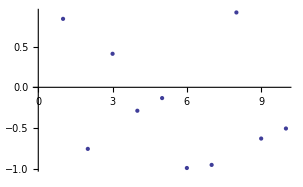

```mathematica
ListPlot[ssq]
```

```mathematica
f[x_,y_]:=Sin[2 Pi x y];
Short[data=Flatten[
Table[{{x,y},f[x,y]},{x,0.,1.,.1},{y,0.,1.,.1}],1]]
```

{{{0.,0.},0.},«119»,{{1.,1.},-2.44921×10^-16}}

```mathematica
ifun=Interpolation[data]
```

InterpolatingFunction[{{0.,1.},{0.,1.}},<>]

```mathematica
Plot3D[ifun[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
ListPlot3D[Map[Flatten,data]]
```

-Graphics3D-

```mathematica
list={1,0,1,0,0,1,0,0,0,1};
```

```mathematica
slist=SparseArray[list]
```

SparseArray[<4>,{10}]

```mathematica
slist==list
```

True

```mathematica
slist+3==list+3
```

True

```mathematica
slist+3
```

SparseArray[<4>,{10},3]

```mathematica
Sin[N[slist]]==Sin[N[list]]
```

True

```mathematica
slist===list
```

False

```mathematica
Normal[slist]
```

{1,0,1,0,0,1,0,0,0,1}

```mathematica
%===list
```

True